```mathematica
(* bullet principle axis transformation
https://github.com/bulletphysics/bullet3/blob/cdd56e46411527772711da5357c856a90ad9ea67/src/BulletCollision/CollisionShapes/btCompoundShape.cpp#L202 *)

(* bullet physics merge contacts 
https://github.com/bulletphysics/bullet3/blob/4a66d6c80b38a87ecbdf2fd5c4d281f0b5913d22/src/BulletCollision/Gimpact/btContactProcessing.cpp#L145 *)

(* bullet physics diagonalize 
https://github.com/bulletphysics/bullet3/blob/4a66d6c80b38a87ecbdf2fd5c4d281f0b5913d22/src/LinearMath/btMatrix3x3.h#L693 *)
```

```mathematica
SetDirectory[NotebookDirectory[]<>"../"];
<<RLBot`
SetDirectory[NotebookDirectory[]];
```

```mathematica
OverlappingQ[c_,b_, R_]  :=( Norm[nearestPointOnHitbox[c, b["location"]]-b["location"]]<= R)
offset = {13.97565993,0.0,20.75498772};
halfwidths=  {59.0,42.1,18.1};
margin = 0;
nearestPointOnHitbox[c_, p_] := Module[{center, x, q},
center  = c["location"] +  c["orientation"].offset;
x = (p - center).c["orientation"];
x = Table[Clip[x[[i]], {-(halfwidths[[i]]-margin), (halfwidths[[i]]-margin)}], {i, 1, 3}];
q = center + c["orientation"].x;
q + margin Normalize[p -q]
]
damping = 0.03144;
g = -650.0;
Δt = 1.0/120.0;
cMass = 180.0;
bMass = 30.0;
cI = cMass({{751, 0, 0}, {0, 1334, 0}, {0, 0, 1836}});
bI = 2/5 bMass RBounce^2({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
RBounce = 91.25;
pushZScale = 0.35;
pushForwardScale = 0.65;
pushFactorCurve[Δv_] := Interpolation[({{0, 0.65}, {500, 0.65}, {2300, 0.55}, {4600, 0.30}}), InterpolationOrder->1][Δv]
```

```mathematica
OBB[c_] := Module[{p, w, o, vertices},
o = c["orientation"];
w = halfwidths;
p = c["location"] + o.offset;
vertices =(#+p)& /@( ({{-1, -1, -1}, {1, -1, -1}, {-1, 1, -1}, {1, 1, -1}, {-1, -1, 1}, {1, -1, 1}, {-1, 1, 1}, {1, 1, 1}}).DiagonalMatrix[w].Transpose[o]);
Polygon[vertices[[#]]]& /@ ({{1, 2, 4, 3}, {2, 4, 8, 6}, {4, 3, 7, 8}, {3, 1, 5, 7}, {1, 2, 6, 5}, {5, 6, 8, 7}})
]
collide[c_, b_] := Module[{info = <||>, cAfter=c,bAfter=b,n1,n2,p,paraScale,normalaxis, combinedaxis,Δv1,Δv1perp,Δv1para,J1para, J1perp,J1,Δv2,J2,f},
o = c["orientation"];
f = o[[All, 1]];
p = nearestPointOnHitbox[c, b["location"]];
n1=Normalize[p-b["location"]];
Δv1=(c["velocity"]+Cross[c["angular_velocity"],p-c["location"]])-(b["velocity"]+Cross[b["angular_velocity"],p-b["location"]]);

L = p-c["location"];
bΩ = Ω[p-b["location"]];
cΩ = Ω[p-c["location"]];
A = (1/cMass+1/bMass)IdentityMatrix[3] - bΩ.Inverse[bI].bΩ  - cΩ.o.Inverse[cI].Transpose[o].cΩ ;
J1 = LinearSolve[A, Δv1];
J1perp = Min[(J1.n1), -1.0]n1;
J1para = J1-J1perp;
J1  = J1perp + Min[1, 2 Norm[J1perp]/Norm[J1para]]J1para;

Δv2=c["velocity"]-b["velocity"];
n2=Normalize[(b["location"]-c["location"])*{1,1,pushZScale}];
n2=Normalize[n2-(1-pushForwardScale)(f.n2)f];
J2=bMass n2 Norm[Δv2] pushFactorCurve[Norm[Δv2]];

cAfter["velocity"]+=-J1/cMass + {0, 0, g Δt};
bAfter["velocity"]+=(J1+J2)/bMass + {0, 0, g Δt} - damping b["velocity"]Δt;
bAfter["angular_velocity"]+=LinearSolve[bI, Cross[p-b["location"],J1]];
If[Norm[bAfter["angular_velocity"]] > 6.0, 
bAfter["angular_velocity"] *= 6.0/Norm[bAfter["angular_velocity"]]];

info["p"]=p ;
info["J1"]=J1 ;
info["J2"]=J2 ;
info["n1"]=n1 ;
info["n2"]=n2 ;

{cAfter, bAfter, info}
]
```

```mathematica
ballPredictions[[1]]
```

<|location→{0.,0.,150.},quaternion→{2.6974×10^-6,2.6974×10^-6,2.6974×10^-6,1.},velocity→{2604.9,-0.000925628,636.688},angular_velocity→{-0.0000209807,-1.76683,0.0000910738},orientation→{{1.,-5.39478×10^-6,5.39481×10^-6},{5.39481×10^-6,1.,-5.39478×10^-6},{-5.39478×10^-6,5.39481×10^-6,1.}}|>

```mathematica
ballBefore[[1]]
```

<|location→{0.,0.,150.},quaternion→{2.6974×10^-6,2.6974×10^-6,2.6974×10^-6,1.},velocity→{0.,0.,0.},angular_velocity→{0.,0.,0.},orientation→{{1.,-5.39478×10^-6,5.39481×10^-6},{5.39481×10^-6,1.,-5.39478×10^-6},{-5.39478×10^-6,5.39481×10^-6,1.}}|>

```mathematica
carBefore[[1]]
```

<|location→{-164.13,0.,88.79},quaternion→{2.6974×10^-6,0.0291563,2.6974×10^-6,0.999575},velocity→{1835.87,0.,372.271},angular_velocity→{0.,3.78721,0.},orientation→{{0.9983,-5.23521×10^-6,0.0582877},{5.5498×10^-6,1.,-5.23521×10^-6},{-0.0582877,5.5498×10^-6,0.9983}}|>

```mathematica
L
```

{58.22,0.000237532,12.1379}

```mathematica
cΩLocal = Ω[L.o]
```

{{0,-38.855,0.000467761},{38.855,0,45.0243},{-0.000467761,-45.0243,0}}

```mathematica
cΩLocal.Inverse[cI].cΩLocal
```

{{-0.00628731,-6.37275×10^-8,-0.00728561},{-6.37275×10^-8,-0.0173022,1.34449×10^-7},{-0.00728561,1.34449×10^-7,-0.00844241}}

```mathematica
cΩ.Transpose[o].Inverse[cI].o.cΩ
```

{{-0.000613563,7.83303×10^-8,0.00294298},{7.83303×10^-8,-0.0232664,7.95943×10^-8},{0.00294298,7.95943×10^-8,-0.0141162}}

```mathematica
cΩ.o.Inverse[cI].Transpose[o].cΩ
```

{{-0.000613563,8.33793×10^-8,0.00294298},{8.33793×10^-8,-0.0173022,-6.13384×10^-8},{0.00294298,-6.13384×10^-8,-0.0141162}}

```mathematica
cΩ.o.Inverse[cI].Transpose[o].cΩ
```

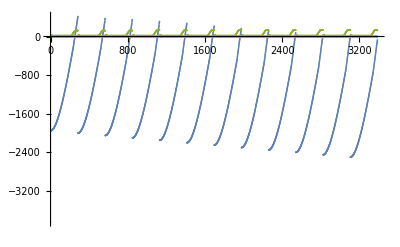

```mathematica
{frame, ball, inputs, car} = ImportPhysicsTickJSONEpisode["dodges.json"];
ListPlot[Transpose[#["location"] & /@ car]]
```

```mathematica
v = #["velocity"]& /@ball;
Δv= v[[2;;-1]]-v[[1;;-2]];
bounces = {};
Do[
If[OverlappingQ[car[[i]],ball[[i]], 1.1 RBounce]  &&
Norm[Δv[[i]]] > 60.0 &&
frame[[i+1]]-frame[[i]]==1,
AppendTo[bounces, i]
],
{i, 1, Length[frame]-1}
];
numBounces = Length[bounces];
bounces
carBefore = car[[bounces]];
carAfter = car[[bounces+1]];
ballBefore = ball[[bounces]];
ballAfter = ball[[bounces+1]];
```

{240,527,811,1096,1382,1670,1955,2240,2525,2810,3095,3381}

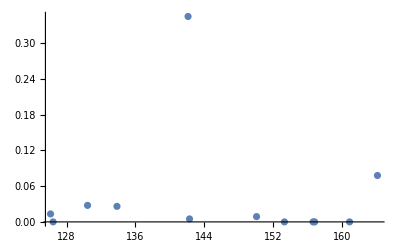

```mathematica
margin = 0;
{carPredictions, ballPredictions, info}=Transpose[Table[collide[carBefore[[i]], ballBefore[[i]]], {i, 1, numBounces}]];
errors = (#["angular_velocity"]&/@ ballPredictions)-(#["angular_velocity"]&/@ ballAfter);
Δx = (#["location"]&/@ ballBefore)-(#["location"]&/@ carBefore);
θ = ArcCos[#["orientation"][[3,1]]]&/@ carBefore;
ListPlot[Transpose[{Norm[#[[1;;2]]]& /@ Δx, (Norm /@ errors)/(Norm[#["angular_velocity"]]&/@ ballAfter)}], PlotRange->All]
```

```mathematica
((#["velocity"]&/@ ballPredictions) - (#["velocity"]&/@ ballAfter))/(Norm /@ ((#["velocity"]&/@ ballAfter) - (#["velocity"]&/@ ballBefore)))
(#["velocity"]&/@ ballAfter) - (#["velocity"]&/@ ballBefore)
```

{{0.0162234,-0.0212301,0.00376406},{0.0265018,-0.0304643,0.0118524},{-0.0145195,0.0272295,0.00653917},{-0.00594239,0.0157936,0.00815165},{0.0111264,0.0069756,0.009704},{-0.00974665,0.0163841,0.00277487},{-0.0000363621,-0.0120956,0.00717789},{-0.0217056,0.0103696,0.00575908},{0.178049,0.226404,-0.505297},{-0.00449887,-0.0211506,0.0106728},{-0.291217,0.326951,-0.614193},{0.0217397,-0.0176938,0.0107027},{-0.0567506,0.224992,-0.147288},{0.0270248,0.0342903,0.00544768},{0.0421864,0.0118741,0.0105235},{0.0325697,-0.0205586,0.0178889},{0.00793391,0.00254604,0.0226638},{0.0236441,-0.0198412,0.0204842},{-0.00913589,0.0212282,0.0121734},{0.0212872,0.0255569,0.00584408},{-0.0055347,0.0169172,0.00441042},{-0.00859099,0.0196318,0.00317655}}

{{-175.83,-159.98,283.942},{-68.94,-45.3,68.982},18,{181.33,-21.3401,134.452},{260.23,133.95,265.012}}
 |  |  |  |

```mathematica
carΔp = cMass((#["velocity"]-{0,0,g Δt}&/@ carAfter) - (#["velocity"]&/@ carBefore));
ballΔp = bMass((#["velocity"]-{0,0,g Δt}&/@ ballAfter)-(#["velocity"]&/@ ballBefore));
momentumChange=(carΔp + ballΔp)
#["J2"]&/@ info
```

{{31740.3,0.,5293.13},{31519.8,0.,6450.53},{31494.,0.,6685.13},{31611.3,0.,5565.83},{31680.6,0.,-5394.07},{31805.7,0.,859.97},{31741.8,0.,4486.13},{-1059.89,0.,2838.26},{31628.7,0.,7909.43},{-1855.8,0.,5081.06},{31338.6,0.,13837.4},{-3019.49,0.,8365.46},{31075.8,0.,13495.1},{-3726.28,0.,10361.4},{-4326.,0.,12038.1},{30625.5,0.,2579.33},{-4656.31,0.,12951.9}}

{{31645.2,-0.0952866,5312.67},{31429.,-0.0902989,6362.39},{31415.4,-0.0775541,6458.55},{31549.2,-0.0600599,5645.53},{31634.8,-0.045995,3865.04},{31787.5,-0.0205773,1174.58},{31747.1,-0.00176206,-1736.34},{16924.5,0.00282507,-1391.5},{31645.3,0.00872422,-3138.22},{19312.1,0.00838864,-2330.2},{31378.5,0.0303092,-5187.31},{19212.2,0.0182691,-3245.1},{31127.,0.0401281,-6429.15},{18444.5,0.023293,-3822.35},{19859.3,0.0363439,-4908.96},{30708.1,0.0741722,-8028.47},{19380.6,0.0489082,-5053.85}}

```mathematica
Norm /@ momentumChange
Norm[#["J2"]]&/@ info
```

{37883.5,26028.6,46357.3,31682.3,18161.,9495.12,12760.2,7744.15,4929.61,8128.82,10643.9,23836.5,22538.4,10693.2,37521.1,38051.2,23026.7,12348.1,7949.74,26593.3,37186.9,16032.7,32556.,74439.5,15762.7,34991.9,31876.7,12700.9,10978.1,8188.83,14610.3,18175.9,10170.2,7342.7,7146.88,29707.2,36334.1,39609.3,33276.,33660.6}

{32198.5,17866.4,30794.2,22417.,12003.8,8372.78,9695.77,6423.45,3443.64,6142.96,9800.67,19915.5,13628.6,6369.67,23940.4,26758.1,17785.3,8482.48,5884.61,26915.9,20261.1,10529.8,28517.5,21329.8,26148.4,24288.7,24748.9,10053.,10893.2,8215.49,13030.1,12661.2,10142.4,7318.58,7127.71,24897.9,36896.8,39507.5,33038.8,33656.9}

```mathematica
xb  = (#["location"]&/@ ballBefore);
Δvb=((#["velocity"]&/@ ballAfter) - (#["velocity"]&/@ ballBefore));
Δωb=((#["angular_velocity"]&/@ ballAfter) - (#["angular_velocity"]&/@ ballBefore));
Ib = 2/5 bMass RBounce^2 IdentityMatrix[3];

xc  = (#["location"]&/@ carBefore);
Δvc=((#["velocity"]&/@ carAfter) - (#["velocity"]&/@ carBefore));
Δωc=((#["angular_velocity"]&/@ carAfter) - (#["angular_velocity"]&/@ carBefore));
Ic = cI;

Δx =(#["location"]&/@ ballBefore)-(#["location"]&/@ carBefore);
Δv =(#["velocity"]&/@ ballBefore)-(#["velocity"]&/@ carBefore);
Δω=(#["angular_velocity"]&/@ ballBefore)-(#["angular_velocity"]&/@ carBefore);


Δvp=((#["velocity"]&/@ ballPredictions) - (#["velocity"]&/@ ballBefore));
```

```mathematica
Max[Abs[Δvp[[All, 1]]/Δvp[[All, 3]]]]
```

0.57483

```mathematica
info[[69]]["n1"]
```

{-5.39481×10^-6,5.39478×10^-6,-1.}

```mathematica
Max[Abs[Δvb[[All, 1]]/Δvb[[All, 3]]]]
```

1.63118

```mathematica
Δvb[[69, 1]]/Δvb[[69, 3]]
```

-1.63118

```mathematica
Ordering[Abs[Δvb[[All, 1]]/Δvb[[All, 3]]],  -1]
```

{69}

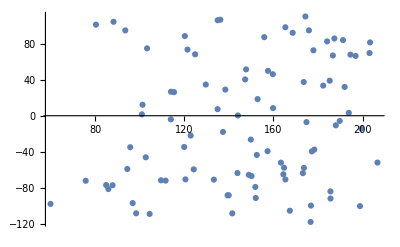

```mathematica
ListPlot[Transpose[{Δvb[[All, 3]], Δvb[[All, 1]]}]]
```

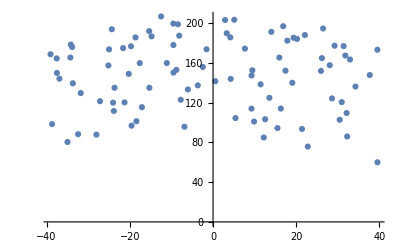

```mathematica
ListPlot[Transpose[{Δx[[All, 1]], Δvb[[All, 3]]}]]
```

```mathematica
Abs[Δvb[[All, 1]]/Δvb[[All, 3]]]
```

{0.479007,0.445686,0.585941,0.545854,0.666899,0.316253,0.342345,0.215599,0.22712,0.905614,0.0165609,0.273573,0.348362,0.645092,0.333205,0.364909,0.249959,0.289425,0.337113,0.00222746,0.427679,0.78515,0.348615,0.631944,0.593864,0.407848,0.73521,0.209541,0.368065,0.947074,0.120247,0.654143,0.358277,0.449202,0.183294,0.629978,0.563997,0.532076,1.1006,0.44212,0.559324,0.438891,0.176591,0.318572,0.878199,0.233441,0.504455,0.0719705,0.179001,0.0529176,0.600217,0.538528,1.00104,0.625738,0.630883,0.723877,0.210656,0.494943,0.040486,0.952507,0.546089,0.452416,0.209859,0.350185,1.25788,0.60447,0.288528,0.633216,1.63118,0.782418,0.0565298,0.44067,0.0150609,0.0304025,0.251516,0.266952,0.223299,0.400074,0.120765,0.448088,0.166455,0.39524,0.0540154,0.457665,1.04318,0.285234,0.0354474,0.520278,1.18159,0.130793,0.765581,1.01252}

```mathematica
Covariance[ArrayFlatten[{{#["angular_velocity"]&/@ ballBefore, Δvb}}]]//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0.
0. | 8.66041 | 0. | 202.922 | 0. | 18.7904
0. | 0. | 0. | 0. | 0. | 0.
0. | 202.922 | 0. | 4773.15 | 0. | 442.237
0. | 0. | 0. | 0. | 0. | 0.
0. | 18.7904 | 0. | 442.237 | 0. | 1302.21)

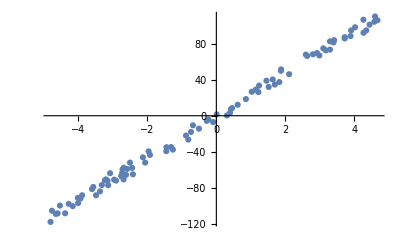

```mathematica
ListPlot[Transpose[{#["angular_velocity"][[2]]&/@ ballBefore, Δvb[[All, 1]]}]]
```

```mathematica
Δvb[[All, 1]]/(#["angular_velocity"][[2]]&/@ ballBefore)
```

{21.9008,24.2619,22.0863,21.5958,24.5323,26.6539,23.8549,20.5144,21.4995,23.191,8.12891,24.6745,27.4315,24.7801,23.7364,24.184,27.1253,26.4333,25.2254,1.05001,26.3239,22.7082,26.1639,23.9714,24.4434,22.9032,22.7428,25.3835,20.7162,22.5975,19.6877,22.186,22.3996,21.6925,26.9973,22.1475,22.0104,23.9453,24.7189,23.3052,23.4597,24.611,32.5392,20.8102,24.6087,25.9306,24.1174,28.4596,24.9923,18.5382,22.7418,21.8188,24.2057,22.8621,22.7078,24.1362,29.8591,23.3399,76.0498,22.8869,24.3748,24.9223,26.7935,21.5119,22.7749,22.2991,21.8674,25.3387,22.8772,25.0107,15.6705,25.0853,148.972,20.669,25.2149,20.4421,20.1798,23.99,21.5579,25.0556,21.0781,26.9036,17.2687,23.0635,23.4384,22.6246,17.6455,22.1654,22.7857,24.4766,23.5735,24.2563}

```mathematica
Δvb[[All, 1]]/Δvb[[All, 3]]
```

{0.164233,0.162274,-0.166512,-0.656552,-0.221242,0.377039,-0.0200333,0.176166,0.224013,-0.186362,-0.237912,-0.0996231,0.261989,0.528252,-0.634884,0.0257081,-0.222065,0.244009,0.206712,-0.0424993,-0.0788507,0.0307083,0.27484,-0.143327,-0.341569,0.00541235,0.325489,0.217573,0.204846,-0.365301,-0.268927,-0.388361,-0.123629,0.297007,0.107435,-0.156379,-0.127165,-0.269894,-0.10915,0.477192,0.392864,-0.310092,0.441751,-0.229633,0.373799,-0.125011,0.00190643,-0.0736911,0.484195,-0.0864368,0.20155,-0.27916,-0.250995,-0.0176953,0.454432,0.350956,-0.20692,0.051622,0.1874,0.542134,-0.110773,-0.0118746,0.292776,-0.047353,0.446473,-0.209978,-0.19261}

```mathematica
k = 5;
Print["Δx: ",Δx[[k]]];
Print["ω: ",Δω[[k]]];
Print["predicted vchange: ",ballPredictions[[k]]["velocity"] - ballBefore[[k]]["velocity"]];
Print["actual vchange: ",ballAfter[[k]]["velocity"] - ballBefore[[k]]["velocity"]];
info[[k]]["n1"]
{value, rule}=NMinimize[{Norm[
bMass Inverse[Ib].Cross[RBounce{n1, n2, n3},Δvb[[k]]] - Δωb[[k]]
],{n1, n2, n3}.{n1, n2, n3}==1
},{n1, n2, n3}] 
info[[k]]["p"]
p = xb[[k]] + RBounce {n1, n2, n3} /. rule
nearestPointOnHitbox[carBefore[[k]], p]
```

Δx: {36.9,0.,131.68}

ω: {0.,-4.12571,0.}

predicted vchange: {-54.8601,-0.00110699,366.244}

actual vchange: {-22.881,0.,283.682}

{5.39478×10^-6,5.39481×10^-6,-1.}

{2.97193×10^-8,{n1→-0.238784,n2→1.18462×10^-9,n3→-0.971073}}

{36.9005,0.000522352,784.855}

{15.1109,1.08096×10^-7,793.07}

{15.111,0.0000444238,784.855}

```mathematica
{-74.0271043140771,-0.004124787878596904,972.7239819179154}-{-99.81099700927734,0.,947.0699920654297}
```

{25.7839,-0.00412479,25.654}

```mathematica
D[Cross[{n1, n2, n3}, {v1, v2, v3}], {{n1, n2, n3}}]
```

```mathematica
Ω[{v1_, v2_, v3_}] := {{0,-v3,v2},{v3,0,-v1},{-v2,v1,0}};
```

```mathematica
testDirection[n_, f_] := Module[{m1, m2, eye =  IdentityMatrix[3], A},
m1=Normalize[n*{1,1,pushZScale}];
m1=Normalize[m1-(1-pushForwardScale)(f.m1)f];

A = (eye-(1-pushForwardScale)Outer[Times, f, f]).({{1, 0, 0}, {0, 1, 0}, {0, 0, pushZScale}});
m2 = Normalize[A.n];
{m1, m2}
]
```

```mathematica
i = 69;
c = carBefore[[i]];
b = ballBefore[[i]];
Module[{info = <||>, cAfter=c,bAfter=b,n1,n2,p,paraScale,normalaxis, combinedaxis,Δv1,Δv1perp,Δv1para,J1para, J1perp,J1,Δv2,J2, o, f},
o = c["orientation"];
Print[o];
p = nearestPointOnHitbox[c, b["location"]];

n1=Normalize[p-b["location"]];
Δv1=(c["velocity"]+Cross[c["angular_velocity"],p-c["location"]])-(b["velocity"]+Cross[b["angular_velocity"],p-b["location"]]);

Print[Δv1];
Print[p-b["location"]];

bΩ = Ω[p-b["location"]];
cΩ = Ω[p-c["location"]];
A = (1/cMass+1/bMass)IdentityMatrix[3] - bΩ.Inverse[bI].bΩ  - cΩ.Inverse[cI].cΩ ;
J1 = LinearSolve[A, Δv1];
J1perp = (J1.n1)n1;
J1para = J1-(J1.n1)n1;
J1  = J1perp + Min[1, 2 Norm[J1perp]/Norm[J1para]]J1para;

J2 = {0, 0,0};
cAfter["velocity"]+=-J1/cMass + {0,0,g Δt};
bAfter["velocity"]+=(J1+J2)/bMass + {0,0,g Δt} - damping b["velocity"]Δt;

Print["predicted: ",J1/bMass];
Print["exact: ",Δvb[[i]]];
]
```

{{1.,-5.39478×10^-6,5.39481×10^-6},{5.39481×10^-6,1.,-5.39478×10^-6},{-5.39478×10^-6,5.39481×10^-6,1.}}

{-403.277,0.,101.053}

{-0.000508543,0.00050854,-94.2652}

predicted: {-97.3524,-0.000181606,60.4903}

exact: {-97.871,0.,60.}

```mathematica
Ω[{a1, a2, a3}].DiagonalMatrix[{s1, s2, s3}].Ω[{a1, a2, a3}] // MatrixForm
```

(-a3^2 s2-a2^2 s3 | a1 a2 s3 | a1 a3 s2
a1 a2 s3 | -a3^2 s1-a1^2 s3 | a2 a3 s1
a1 a3 s2 | a2 a3 s1 | -a2^2 s1-a1^2 s2)

```mathematica
cΩ
```

{{0,-12.1379,0.000237532},{12.1379,0,-58.22},{-0.000237532,58.22,0}}

```mathematica
L
```

{58.22,0.000237532,12.1379}

```mathematica
Outer[Times, L, L]
```

{{3389.57,0.0138291,706.669},{0.0138291,5.64213×10^-8,0.00288314},{706.669,0.00288314,147.329}}

```mathematica
cΩ.cΩ
```

{{-147.329,0.0138291,706.669},{0.0138291,-3536.9,0.00288314},{706.669,0.00288314,-3389.57}}

```mathematica
LookAt[n_] := Module[{f, l, u},
f = Normalize[n];
l = Normalize[Cross[{0, 0, 1}, f]];
u = Normalize[Cross[f, l]];
Transpose[{f, l, u}]
]
```

```mathematica
b = ballBefore[[1]];
b["location"] = {917.720764, 2551.711670, 1240.823242};
b["velocity"] = {196.716019,-23.094584,-770.718506};
b["angular_velocity"] = {0, 0, 0};
```

```mathematica
goal = {0, 5120, 300};
desiredDirection = Normalize[goal - b["location"]];
```

```mathematica
target = b["location"];
```

```mathematica
c = carBefore[[1]];
c["location"] = target;
c["velocity"] = {894.270935, 1425.313965,-144.948380};
c["angular_velocity"] = {0, 0, 0};
c["orientation"] = LookAt[Normalize[c["velocity"]]];
```

```mathematica
objective[dx_, dy_, dz_] := Module[{},
c["location"] = target + {dx, dy, dz};
Do[
If[OverlappingQ[c, b, 93.15], c["location"] -= c["velocity"] Δt]
,
{i, 1, 60}
];
c["location"] += c["velocity"] Δt;

{carPrediction, ballPrediction, info} = collide[c, b];
{ballPrediction, ArcCos[Normalize[ballPrediction["velocity"][[1;;2]]].desiredDirection[[1;;2]]]}
]
```

```mathematica
dx = 0;
dy = 0;
dz = 0;
```

```mathematica
ϵ = 0.01;
```

```mathematica
Do[
f = objective[dx,dy,dz][[2]];
gradf = 1/ϵ({
objective[dx+ϵ,dy,dz][[2]],
objective[dx,dy+ϵ,dz][[2]],
objective[dx,dy,dz+ϵ][[2]]
}-f);

{dx, dy, dz} -= 5Normalize[gradf];
If[Norm[{dx, dy, dz}] > 90, {dx, dy, dz} *= 90/Norm[{dx, dy, dz}]];
Print[{f, {dx, dy, dz}}]
,
{15}
]
```

{0.563839,{87.3916,-21.4986,-0.724862}}

{0.563739,{87.4612,-21.2133,-0.727441}}

{0.56365,{87.5262,-20.9437,-0.730184}}

{0.56357,{87.5867,-20.6891,-0.733064}}

{0.563499,{87.6431,-20.4486,-0.736058}}

{0.563436,{87.6957,-20.2215,-0.739143}}

{0.563379,{87.7449,-20.0072,-0.7423}}

{0.563329,{87.7907,-19.8048,-0.745511}}

{0.563285,{87.8336,-19.6137,-0.74876}}

{0.563245,{87.8737,-19.4334,-0.752033}}

{0.563209,{87.9111,-19.2632,-0.755317}}

{0.563178,{87.9461,-19.1026,-0.758601}}

{0.56315,{87.9789,-18.951,-0.761874}}

{0.563125,{88.0095,-18.808,-0.765127}}

{0.563102,{88.0382,-18.673,-0.768352}}

```mathematica
Graphics3D[{
Point[goal],
Arrow[{b["location"], b["location"] + b["velocity"]}],
Arrow[{b["location"], b["location"] + ballPrediction["velocity"]}],
Sphere[b["location"], 93.15],
OBB[c],
Arrow[{c["location"], c["location"] + c["velocity"]}]
}]
```

-Graphics3D-

```mathematica
o = c["orientation"]
```

{{1/(3 √3),-5/(√26),0},{5/(3 √3),1/(√26),0},{1/(3 √3),0,1}}

```mathematica
o.Transpose[o]
```

{{701/702,-5/702,1/27},{-5/702,677/702,5/27},{1/27,5/27,28/27}}